```mathematica
f[x_,y_]:=Sqrt[2/Pi]*Exp[-(x)^2]*Exp[-(y)^2]
```

```mathematica
Integrate[f[x,y]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

1

```mathematica
fs[x_,y_]:=Evaluate[Integrate[f[x,y]^2,{x,-Infinity,Infinity}]*Integrate[f[x,y]^2,{y,-Infinity,Infinity}]]
```

```mathematica
Integrate[fs[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

1

```mathematica
e[x_,y_]:=Evaluate[f[x,y]^2-fs[x,y]]
```

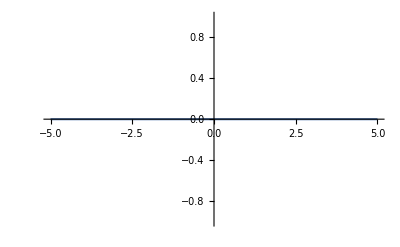

```mathematica
Plot[e[x,0]^2,{x,-5,5}]
```

```mathematica
Plot[e[x,-1],{x,-5,5}]
```

-Graphics-

```mathematica
NIntegrate[e[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

0.254464

```mathematica
f[x,y]^2
```

((ⅇ^(-(1+x)^2-(-1+y)^2)+ⅇ^(-(-1+x)^2-(1+y)^2))^2)/((1+1/ⅇ^4) π)

```mathematica
Integrate[f[x,y]^2,{x,-Infinity,Infinity}]
```

(ⅇ^(-2 y^2) √(2/π) (1+ⅇ^2 Cosh[4 y]))/(1+ⅇ^4)

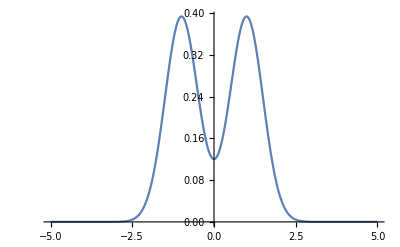

```mathematica
Plot[%10,{y,-5,5}]
```